```mathematica
AB=l1=93.75;
BC=l2=421.875;
h=187.5;
α=0.22409309230137084;
CD=l3=195.;
ls2=0.3BC;
ls3=0.3BC;
pmax=8 10^5;
pmin=-8 10^4;
m2=12;
m3=7.8;
Js2=0.214;
iSize=400;
d4=0.05;
d3=0.018;
g=9.81;
n1=1.6;
w1sr=2Pi n1;
δ=1/20;
```

```mathematica
ls2
ls3
JprI
Mprdv
```

126.563

126.563

15.6464

78.9075

```mathematica
phi2[x_]:=ArcSin[-l1/l2 Sin[x]]
Rb[x_]:={AB Cos[x],AB Sin[x],0}
Rc[x_]:={AB Cos[x]+BC Cos[phi2[x]],AB Sin[x]+BC Sin[phi2[x]],0}
Rd[x_]:=Rc[x]+{CD,0,0}
Rs2[x_]:={AB Cos[x]+ls2  Cos[phi2[x]],AB Sin[x]+ls2 Sin[phi2[x]],0}
Rs3[x_]:=Rc[x]+{ls3,0,0}
```

```mathematica
Animate[
pA:={0,0};
pB:=Rb[ϕ][[1;;2]];
pC:=Rc[ϕ][[1;;2]];
pD:=Rd[ϕ][[1;;2]];
pS3:=Rs3[ϕ][[1;;2]];
pS2:=Rs2[ϕ][[1;;2]];
Graphics[{Line[{pA,pB}],Line[{pB,pC}],Line[{pC,pD}],Point[pS2],Point[pS3],
Line[{pD-{0,100},pD+{0,100},pD+{60,100},pD+{60,-100},pD-{0,100}}],
Circle[#,5]&/@{pA,pB,pC},
FontSize->14,Text[#[[1]],#[[2]] +{15,15}]&/@{ {"A",pA}, {"B",pB}, {"C",pC},{"S3",pS3},{"S2",pS2},{"D",pD}}


},
Axes->False,PlotRange->{{-AB-5,AB+BC+CD+75},{-AB-50,AB+50}}],{ϕ,0,4Pi}]
```

```mathematica
Vb[x_]:=(D[Rb[y],y]/.y->x)[[1;;2]]
Vc[x_]:=(D[Rc[y],y]/.y->x)[[1;;2]]
Vd[x_]:=(D[Rd[y],y]/.y->x)[[1;;2]]
Vs3[x_]:=(D[Rs3[y],y]/.y->x)[[1;;2]]
Vs2[x_]:=(D[Rs2[y],y]/.y->x)[[1;;2]]
```

```mathematica
ab[x_]:=(D[Rb[y],{y,2}]/.y->x)[[1;;2]]
ac[x_]:=(D[Rc[y],{y,2}]/.y->x)[[1;;2]]
ad[x_]:=(D[Rd[y],{y,2}]/.y->x)[[1;;2]]
as3[x_]:=(D[Rs3[y],{y,2}]/.y->x)[[1;;2]]
as2[x_]:=(D[Rs2[y],{y,2}]/.y->x)[[1;;2]]
```

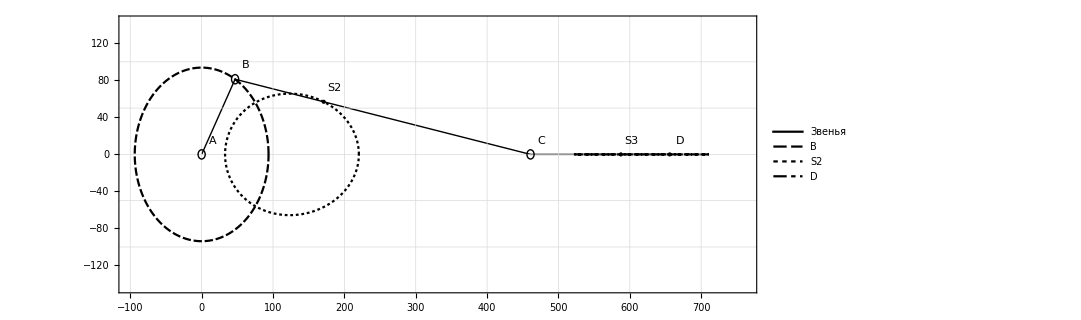

```mathematica
Module[{pA,pB,pC,pD,pS3,pS2,ϕ},
pA:={0,0};
pB:=Rb[ϕ][[1;;2]];
pC:=Rc[ϕ][[1;;2]];
pD:=Rd[ϕ][[1;;2]];
pS3:=Rs3[ϕ][[1;;2]];
pS2:=Rs2[ϕ][[1;;2]];
ϕ=Pi/3;
Show[{Graphics[{PointSize[Large],Thick,Line[{pA,pB}],Line[{pB,pC}],Line[{pC,pD}],Point[pD],Point[pS2],Point[pS3],

Circle[#,5]&/@{pA,pB,pC},
FontSize->14,Text[#[[1]],#[[2]] +{15,15}]&/@{ {"A",pA}, {"B",pB}, {"C",pC},{"S3",pS3},{"S2",pS2},{"D",pD}}


}],
ParametricPlot[{{0,0},Rb[x][[1;;2]],Rs2[x][[1;;2]],Rd[x][[1;;2]]},{x,0,2Pi},PlotTheme->"Monochrome",PlotLegends->{"Звенья","B","S2","D","S2","S3"}]
},
Axes->False,Frame->True,GridLines->{Table[100n,{n,-1,10}],Table[50n,{n,-5,5}]},ImageSize->iSize+400,PlotRange->{{-AB-5,AB+BC+CD+50},{-AB-50,AB+50}}]]
```

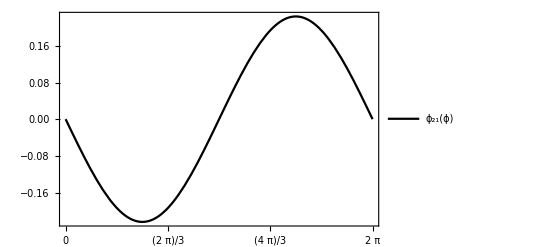

```mathematica
op={Table[Pi /3i,{i,0,8}],Automatic};
Plot[phi2[x],{x,0,2Pi},Frame->True,GridLines->op,FrameTicks->op,PlotTheme->"Monochrome",ImageSize->iSize,PlotLegends->{"ϕ_21(ϕ)"}]
```

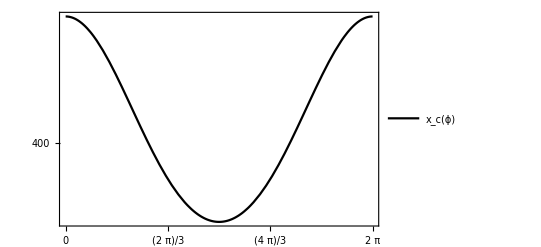

```mathematica
Plot[Rc[x][[1]],{x,0,2Pi},Frame->True,ImageSize->iSize,FrameTicks->{Table[Pi /3i,{i,0,8}],Table[50i,{i,0,20}]},GridLines->{Table[Pi /3i,{i,0,8}],Table[50i,{i,0,12}]},PlotTheme->"Monochrome",PlotLegends->{"x_c(ϕ)"}]
```

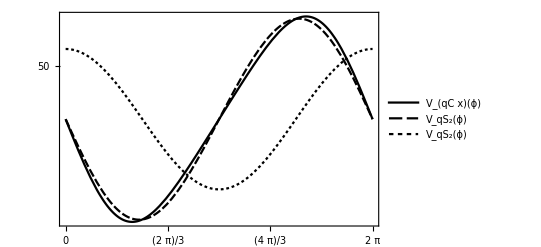

```mathematica
Plot[{Vc[x][[1]],Vs2[x][[1]],Vs2[x][[2]]},{x,0,2Pi},Frame->True,FrameTicks->{Table[Pi /3i,{i,0,8}],Table[50i,{i,-8,8}]},GridLines->{Table[Pi /3i,{i,0,8}],Table[25i,{i,-10,12}]},ImageSize->iSize,PlotTheme->"Monochrome",PlotLegends->{"V_(qC x)(ϕ)","V_qS_2(ϕ)","V_qS_2(ϕ)"}]
```

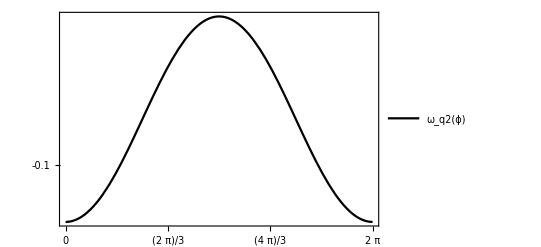

```mathematica
Plot[D[phi2[x],x]/.x->y,{y,0,2Pi},Frame->True,FrameTicks->{Table[Pi /3i,{i,0,8}],Table[0.1i,{i,-10,100}]},GridLines->{Table[Pi /3i,{i,0,8}],Table[0.1i,{i,-10,12}]},ImageSize->iSize,PlotTheme->"Monochrome",PlotLegends->{"ω_q2(ϕ)"}]
```

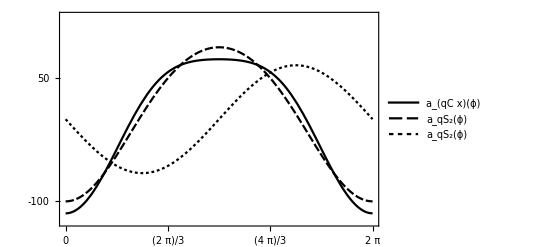

```mathematica
Plot[{ac[x][[1]],as2[x][[1]],as2[x][[2]]},{x,0.001,2Pi-0.001},Frame->True,FrameTicks->{Table[Pi /3i,{i,0,8}],Table[50i,{i,-8,8}]},GridLines->{Table[Pi /3i,{i,0,8}],Table[25i,{i,-10,12}]},PlotRange->125,ImageSize->iSize,PlotTheme->"Monochrome",ClippingStyle->Red,PlotLegends->{"a_(qC x)(ϕ)","a_qS_2(ϕ)","a_qS_2(ϕ)"}]
```

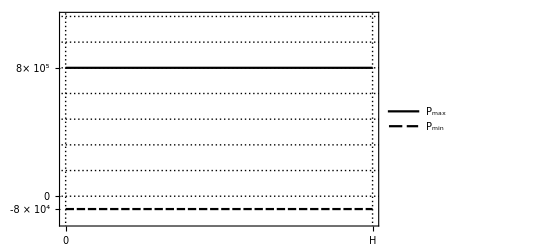

```mathematica
Plot[{10,-1},{x,0,h},Frame->True,GridLines->{{0,h},Table[2i,{i,0,10}]},ExclusionsStyle->Red,FrameTicks->{{0,{h,"H"}},{{-1,"-8 × 10^4"},0,{10,"8× 10^5"}}},PlotRange->{-2,14},PlotTheme->"Monochrome",PlotLegends->{"P_max","P_min"}]
```

```mathematica
Jpr2[x_]:=Js2 (D[phi2[y],y]/.y->x)^2+m2 ((Vs2[x][[1]])^2+(Vs2[x][[2]])^2)/10^6
Jpr3[x_]:=m3 ((Vs3[x][[1]])^2+(Vs3[x][[2]])^2)/10^6
JprII[x_]:=Jpr2[x]+Jpr3[x]
```

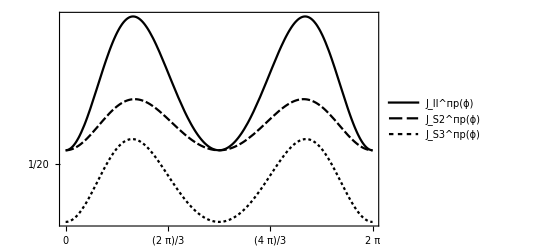

```mathematica
Plot[{JprII[x],Jpr2[x],Jpr3[x]},{x,0,2Pi},Frame->True,FrameTicks->{Table[Pi /3i,{i,0,8}],Table[5/100i,{i,-8,100}]},GridLines->{Table[Pi /3i,{i,0,8}],Table[5/100i,{i,-10,12}]},ImageSize->iSize,PlotTheme->"Monochrome",ClippingStyle->Red,PlotLegends->{"J_II^(:043f:0440)(ϕ)","J_S2^(:043f:0440)(ϕ)","J_S3^(:043f:0440)(ϕ)"}]
```

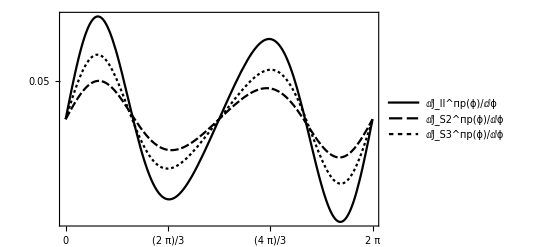

```mathematica
Plot[{D[JprII[x],x]/.x->z,D[Jpr2[x],x]/.x->z,D[Jpr3[x],x]/.x->z},{z,0,2Pi},Frame->True,FrameTicks->{Table[Pi /3i,{i,0,8}],Table[0.05i,{i,-8,100}]},GridLines->{Table[Pi /3i,{i,0,8}],Table[0.05i,{i,-10,12}]},ImageSize->iSize,PlotTheme->"Monochrome",ClippingStyle->Red,PlotLegends->{"ⅆJ_II^(:043f:0440)(ϕ)/ⅆϕ","ⅆJ_S2^(:043f:0440)(ϕ)/ⅆϕ","ⅆJ_S3^(:043f:0440)(ϕ)/ⅆϕ"}]
```

```mathematica
s[x_]:=Rd[0][[1]]-Rd[x][[1]]
```

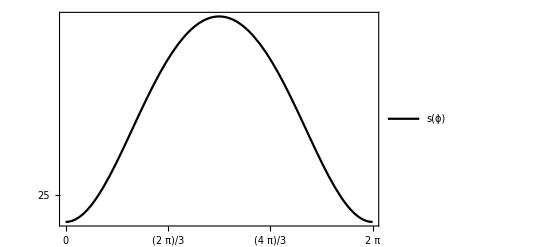

```mathematica
Plot[s[z],{z,0,2Pi},Frame->True,FrameTicks->{Table[Pi /3i,{i,0,8}],Table[25i,{i,-8,100}]},GridLines->{Table[Pi /3i,{i,0,8}],Table[25i,{i,-10,12}]},ImageSize->iSize,PlotTheme->"Monochrome",ClippingStyle->Red,PlotLegends->{"s(ϕ)"}]
```

```mathematica
p[x_]:=Piecewise[{{pmax,1Pi≤x≤2Pi},{pmin,0≤ x<1Pi}}]
Fc[x_]:=Piecewise[{{-pmax Pi d4^2/4-pmin Pi/4(d4^2-d3^2) ,1Pi≤x≤2Pi},{+pmax Pi/4(d4^2-d3^2)+pmin Pi/4 d4^2,0≤ x<1Pi}}]
```

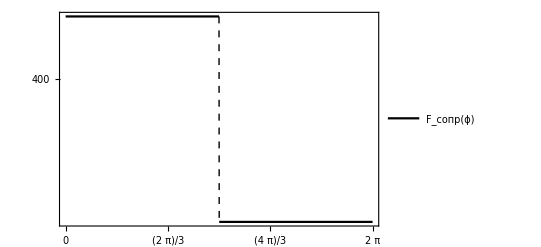

```mathematica
Plot[Fc[z],{z,0,2Pi},Frame->True,FrameTicks->{Table[Pi /3i,{i,0,8}],Table[400i,{i,-8,100}]},GridLines->{Table[Pi /3i,{i,0,8}],Table[400i,{i,-10,12}]},ImageSize->iSize,PlotTheme->"Monochrome",ExclusionsStyle->Dashed,PlotLegends->{"F_(:0441:043e:043f:0440)(ϕ)"}]
```

```mathematica
Mprc[x_]:={Fc[x],0}. Vc[x]/1000
MprG2[x_]:={0,-m2 g}.Vs2[x]/1000
Mprsopr[x_]:=Mprc[x]+MprG2[x]
```

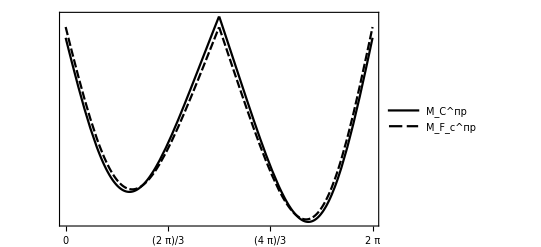

```mathematica
Plot[{Mprsopr[x],Mprc[x]},{x,0,2Pi},Frame->True,FrameTicks->{Table[Pi /3i,{i,0,8}],Table[25i,{i,-8,100}]},GridLines->{Table[Pi /3i,{i,0,8}],Table[25i,{i,-10,12}]},ImageSize->iSize,PlotTheme->"Monochrome",ClippingStyle->Red,PlotLegends->{"M_(:0421)^(:043f:0440)","M_F_c^(:043f:0440)"}]
```

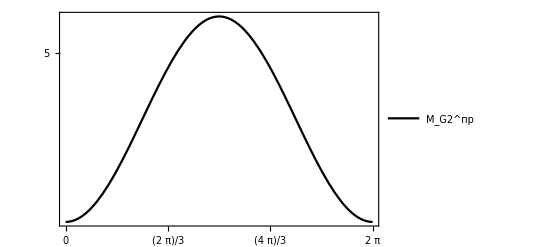

```mathematica
Plot[{MprG2[x]},{x,0,2Pi},Frame->True,FrameTicks->{Table[Pi /3i,{i,0,8}],Table[5i,{i,-8,100}]},GridLines->{Table[Pi /3i,{i,0,8}],Table[5i,{i,-10,12}]},ImageSize->iSize,PlotTheme->"Monochrome",ClippingStyle->Red,PlotLegends->{"M_G2^(:043f:0440)","M_G3^(:043f:0440)"}]
```

```mathematica
Ac:=Integrate[Mprsopr[x],{x,0,2Pi}]
Ac
```

-495.79

```mathematica
Mprdv=-Ac/(2Pi)
```

78.9075

```mathematica
MprS[x_]:=Mprdv+Mprsopr[x]
```

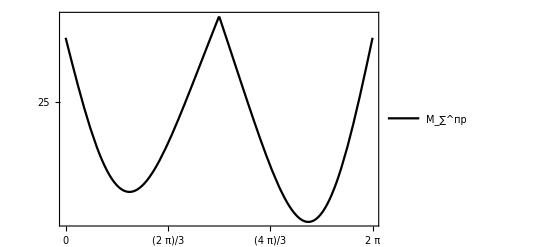

```mathematica
Plot[MprS[z],{z,0,2Pi},Frame->True,FrameTicks->{Table[Pi /3i,{i,0,8}],Table[25i,{i,-8,100}]},GridLines->{Table[Pi /3i,{i,0,8}],Table[25i,{i,-10,12}]},ImageSize->iSize,PlotTheme->"Monochrome",ClippingStyle->Red,PlotLegends->{"M_∑^(:043f:0440)"}]
```

```mathematica
Asum[x_]:=Evaluate[Integrate[MprS[z],{z,0,x},Assumptions->x∈Reals]]
```

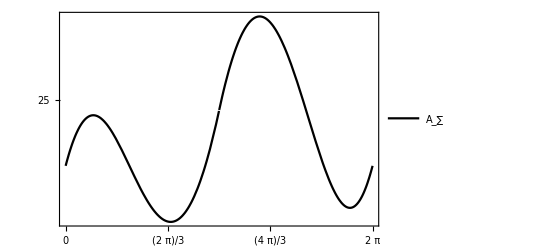

```mathematica
Plot[Asum[k],{k,0,2Pi},Frame->True,FrameTicks->{Table[Pi /3i,{i,0,8}],Table[25i,{i,-8,100}]},GridLines->{Table[Pi /3i,{i,0,8}],Table[25i,{i,-10,12}]},ImageSize->iSize,PlotTheme->"Monochrome",ClippingStyle->Red,PlotLegends->{"A_∑"}]
```

```mathematica
Tii[x_]:=JprII[x]w1sr^2/2
```

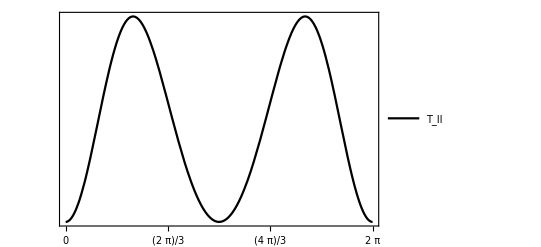

```mathematica
Plot[Tii[k],{k,0,2Pi},Frame->True,FrameTicks->{Table[Pi /3i,{i,0,8}],Table[i,{i,-8,100}]},GridLines->{Table[Pi /3i,{i,0,8}],Table[i,{i,-10,12}]},ImageSize->iSize,PlotTheme->"Monochrome",ClippingStyle->Red,PlotLegends->{"T_II"}]
```

```mathematica
dTi[x_]:=Asum[x]-Tii[x]
```

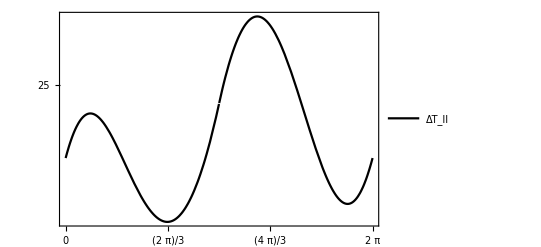

```mathematica
Plot[dTi[k],{k,0,2Pi},Frame->True,FrameTicks->{Table[Pi /3i,{i,0,8}],Table[25i,{i,-8,100}]},GridLines->{Table[Pi /3i,{i,0,8}],Table[25i,{i,-10,12}]},ImageSize->iSize,PlotTheme->"Monochrome",ClippingStyle->Red,PlotLegends->{"ΔT_II"}]
```

```mathematica
Timax=Maximize[{dTi[x],0≤x≤2Pi},x][[1]];
Timin=Minimize[{dTi[x],0≤x≤2Pi},x][[1]];
maxdTi=Timax-Timin
```

79.0649

```mathematica
JprI=maxdTi/(w1sr^2 δ)
```

15.6464

```mathematica
dw1[x_]:=(dTi[x]-(Timax+Timin)/2)/(w1sr JprI)
w1[x_]:=w1sr+dw1[x]
```

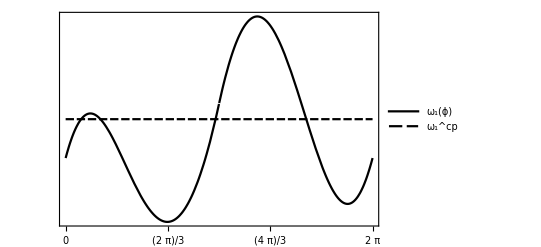

```mathematica
Plot[{w1[k],w1sr},{k,0,2Pi},Frame->True,FrameTicks->{Table[Pi /3i,{i,0,8}],N@Table[1/10i,{i,-8,1000}]},GridLines->{Table[Pi /3i,{i,0,8}],Table[1/10i,{i,-10,120}]},ImageSize->iSize,PlotTheme->"Monochrome",ClippingStyle->Red,PlotLegends->{"ω_1(ϕ)","ω_1^(:0441:0440)"}]
```

```mathematica
ϵ[x_]:=MprS[x]/(JprII[x]+JprI)-w1[x]^2/(2(JprII[x]+JprI))D[JprII[z],z]/.z->x
```

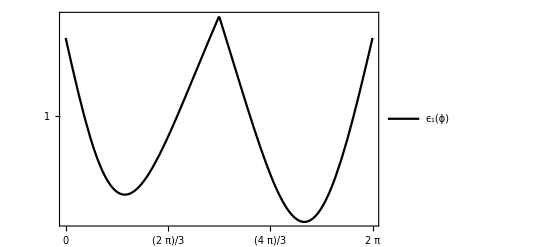

```mathematica
Plot[ϵ[k],{k,0,2Pi},Frame->True,FrameTicks->{Table[Pi /3i,{i,0,8}],Table[1i,{i,-8,1000}]},GridLines->{Table[Pi /3i,{i,0,8}],Table[1i,{i,-10,120}]},ImageSize->iSize,PlotTheme->"Monochrome",ClippingStyle->Red,PlotLegends->{"ϵ_1(ϕ)"}]
```

Расчет маховика

```mathematica
Jdv=0.0025;
J1A=0.025;
z5=18;
z6=21;
JRed=0.02;
u1k=12;
ud1=u1k z6/z5 
JprRed=JRed*ud1^2
Jprdv=Jdv*ud1^2
```

14

3.92

0.49

```mathematica
Jdop=JprI-(JprRed+J1A+Jprdv)
```

11.2114

Маховик - обод со спицами

```mathematica
D2=0.437 Jdop^(1/5)
D1=0.8D2
b=0.2D2
m=6123(D2^2-D1^2)b
```

0.70862

0.566896

0.141724

156.869

Маховик - диск

```mathematica
Dd=0.366 Jdop^(1/5)
bd=0.2Dd
m=1230 Dd^3
```

0.593489

0.118698

257.125

## Силовой расчет